```mathematica
x=.;y=.;r=.; 
L=100;
psi = 3*Pi/4;
a= 10;
b = 10;
c= 10;
r[x_,y_]:={((L/(2psi) )+a  Sin[y])Cos[x], ((L/(2psi) )+b Sin[y] )Sin[x], c Cos[y]};

gx[x_,y_]=Simplify[D[r[x,y],x]];
gy[x_,y_]=Simplify[D[r[x,y],y]];

gxx[x_,y_]:=gx[x,y].gx[x,y];
hx[x_,y_]:=Sqrt[gxx[x,y]];

gyy[x_,y_]:=gy[x,y].gy[x,y];
hy[x_,y_]:=Sqrt[gyy[x,y]];
nx[x_,y_]:=gx[x,y]/hx[x,y];
ny[x_,y_]:=gy[x,y]/hy[x,y];
nz[x_,y_]:=Cross[nx[x,y],ny[x,y]];

tamanho=0.5;

arrow[center_,direc_,color_,size_]:=Module[{dir},dir=Sqrt[3] direc/Sqrt[direc.direc];
Show[Graphics3D[{color,Specularity[Black,20000],EdgeForm[None],Cylinder[{center-tamanho  dir,center+size dir},tamanho/2],Cone[{center+size dir,center+(size+2tamanho) dir},tamanho],Sphere[center,0]},Lighting->"Neutral"]]];
arrowp[center_,direc_,color_]:=Module[{dir},dir=direc;
Show[Graphics3D[{color,Specularity[Black,20000],EdgeForm[None],Cylinder[{center-dir,center+dir},1/3],Cone[{center+2dir,center+2 dir},1.],Sphere[center-dir,0.]},Lighting->"Neutral"]]]

gr2=ParametricPlot3D[r[x,y],{y,0,2*Pi},{x,-psi,psi},Boxed->False];
Show[gr2]
```

-Graphics3D-

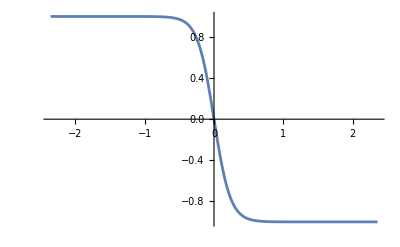

```mathematica
x0=0;
p=5;
ϕ[x_,y_]:=2ArcTan[Exp[(hx[x,y](x-x0))/(p)]];

nzz[x_,y_]:=nz[x,y];
Θ0 = π/2 + 0.2;

θ[x_,y_]:=Θ0 

my[x_,y_]:=Sin[θ[x,y]]*Sin[ϕ[x,y]]*ny[x,y];
mz[x_,y_]:=Cos[θ[x,y]]*nz[x,y];
mx[x_,y_]:=Sin[θ[x,y]]*Cos[ϕ[x,y]]*nx[x,y];
mt[x_,y_]:=mx[x,y]+my[x,y]+mz[x,y];

Plot[Cos [ϕ[x,0]],{x,-psi,psi},PlotRange->Full]
```

```mathematica
Figura=ParametricPlot3D[r[u,v],{u,-psi,psi},{v,0,2*Pi},Mesh->None,Axes->False,PlotPoints->100,Boxed->False,ColorFunction->Function[{x,y,z,u,v},ColorData[{"TemperatureMap",{-1.0,1.0}}][Cos[ϕ[u,v]]]],ColorFunctionScaling->False];



dibujo1=Flatten[Table[arrow[r[x,y],mt[x,y],RGBColor[1.0,0.7,0],tamanho],{x,-psi,psi,Pi/8},{y,0,2*Pi,Pi/10}],1];

Show[Figura,dibujo1,PlotRange->All]
```

-Graphics3D-

```mathematica
(*Definindo a figura com ParametricPlot3D*)Figura=ParametricPlot3D[r[u,v],{u,-psi/90,psi/90},{v,0,2*Pi},Mesh->None,Axes->False,PlotPoints->100,Boxed->False,ColorFunction->Function[{x,y,z,u,v},ColorData[{"TemperatureMap",{-1.0,1.0}}][Cos[θ[u,v]]]],ColorFunctionScaling->False];

(*Definindo os vetores de flecha*)
dibujo1=Flatten[Table[arrow[r[x,y],mt[x,y],RGBColor[1.0,0.7,0],tamanho],{x,-psi/90,psi/90,Pi/6},{y,0,2*Pi,Pi/6}],1];

(*Mostrando a figura com iluminação e sem a caixa de limites*)
Show[dibujo1,PlotRange->All,Boxed->False,Lighting->"Directional",(*Pode ajustar para outras opções como "Classic" ou "Directional"*)ImageSize->800]
```

-Graphics3D-